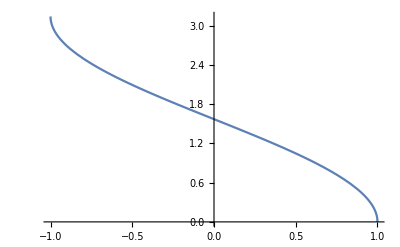

```mathematica
Plot[ArcCos[x],{x,-1,1}]
```

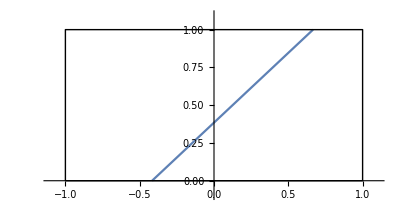

```mathematica
s=.2;
m=1;n=2;

Show[ParametricPlot[{s^(m-n)(1-(1+s^n)t),s^(m-n)(1-(1-s^n)t)},{t,(1-s^(n-m))/(1-s^n),Min[1/(1-s^n),(1+s^(n-m))/(1+s^n)]},PlotRange->{{-1.1,1.1},{-.1,1.1}}],Graphics[Line[{{-1,0},{1,0},{1,1},{-1,1},{-1,0}}]]]
Clear[s,m,n]
```

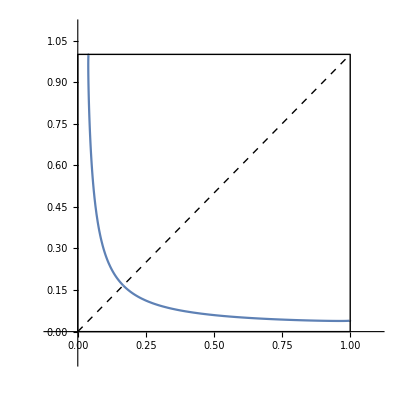

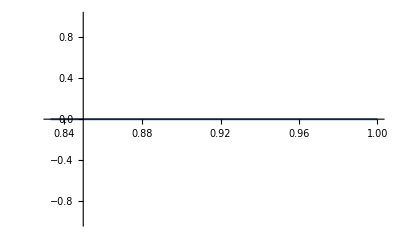

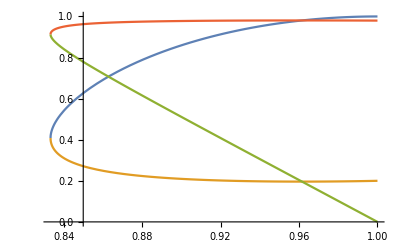

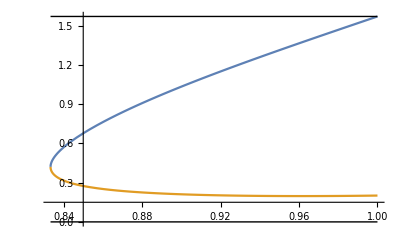

```mathematica
s=.2;
m=1;n=2;

Show[ParametricPlot[{Sin[1/2 ArcCos[(1-(1+s^n)t)/s^(n-m)]+1/2 ArcCos[(1-(1-s^n)t)/s^(n-m)]]^2,Sin[1/2 ArcCos[(1-(1+s^n)t)/s^(n-m)]-1/2 ArcCos[(1-(1-s^n)t)/s^(n-m)]]^2},{t,(1-s^(n-m))/(1-s^n),Min[1/(1-s^n),(1+s^(n-m))/(1+s^n),1]},PlotRange->{{-0.1,1.1},{-.1,1.1}}],
ParametricPlot[{Sin[1/2 ArcCos[(1-(1+s^n)t)/s^(n-m)]-1/2 ArcCos[(1-(1-s^n)t)/s^(n-m)]]^2,Sin[1/2 ArcCos[(1-(1+s^n)t)/s^(n-m)]+1/2 ArcCos[(1-(1-s^n)t)/s^(n-m)]]^2},{t,(1-s^(n-m))/(1-s^n),Min[1/(1-s^n),(1+s^(n-m))/(1+s^n),1]},PlotRange->{{-0.1,1.1},{-.1,1.1}}],Graphics[Line[{{0,0},{1,0},{1,1},{0,1},{0,0}}]],Graphics[{Dashed,Line[{{0,0},{1,1}}]}]]



(*Show[ParametricPlot[{Sin[1/2 ArcCos[(1-(1+s^n)t)/s^(n-m)]+1/2 ArcCos[(1-(1-s^n)t)/s^(n-m)]],Sin[1/2 ArcCos[(1-(1+s^n)t)/s^(n-m)]-1/2 ArcCos[(1-(1-s^n)t)/s^(n-m)]]},{t,(1-s^(n-m))/(1-s^n),Min[1/(1-s^n),(1+s^(n-m))/(1+s^n)]},PlotRange->{{-0.1,1.1},{-.1,1.1}}],Graphics[Line[{{0,0},{1,0},{1,1},{0,1},{0,0}}]],Graphics[{Dashed,Line[{{0,0},{1,1}}]}]]*)


Plot[s^m-s^n Cos[1/2 ArcCos[(1-(1+s^n)t)/s^(n-m)]+1/2 ArcCos[(1-(1-s^n)t)/s^(n-m)]]Cos[1/2 ArcCos[(1-(1+s^n)t)/s^(n-m)]-1/2 ArcCos[(1-(1-s^n)t)/s^(n-m)]]-Sin[1/2 ArcCos[(1-(1+s^n)t)/s^(n-m)]+1/2 ArcCos[(1-(1-s^n)t)/s^(n-m)]]Sin[1/2 ArcCos[(1-(1+s^n)t)/s^(n-m)]-1/2 ArcCos[(1-(1-s^n)t)/s^(n-m)]],{t,(1-s^(n-m))/(1-s^n),Min[1/(1-s^n),(1+s^(n-m))/(1+s^n),1]},PlotRange->{-1,1}]
Plot[{Sin[1/2 ArcCos[(1-(1+s^n)t)/s^(n-m)]+1/2 ArcCos[(1-(1-s^n)t)/s^(n-m)]],Sin[1/2 ArcCos[(1-(1+s^n)t)/s^(n-m)]-1/2 ArcCos[(1-(1-s^n)t)/s^(n-m)]],Cos[1/2 ArcCos[(1-(1+s^n)t)/s^(n-m)]+1/2 ArcCos[(1-(1-s^n)t)/s^(n-m)]],Cos[1/2 ArcCos[(1-(1+s^n)t)/s^(n-m)]-1/2 ArcCos[(1-(1-s^n)t)/s^(n-m)]]},{t,(1-s^(n-m))/(1-s^n),Min[1/(1-s^n),(1+s^(n-m))/(1+s^n),1]},PlotRange->All]
Show[Plot[{1/2 ArcCos[(1-(1+s^n)t)/s^(n-m)]+1/2 ArcCos[(1-(1-s^n)t)/s^(n-m)],1/2 ArcCos[(1-(1+s^n)t)/s^(n-m)]-1/2 ArcCos[(1-(1-s^n)t)/s^(n-m)]},{t,(1-s^(n-m))/(1-s^n),Min[1/(1-s^n),(1+s^(n-m))/(1+s^n),1]},PlotRange->All],Graphics[Line[{{(1-s^(n-m))/(1-s^n),0},{Min[1/(1-s^n),(1+s^(n-m))/(1+s^n),1],0}}]],Graphics[Line[{{(1-s^(n-m))/(1-s^n),π/2},{Min[1/(1-s^n),(1+s^(n-m))/(1+s^n),1],π/2}}]]]

Clear[s,m,n]
```

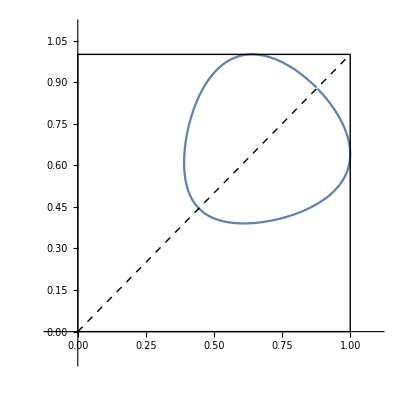

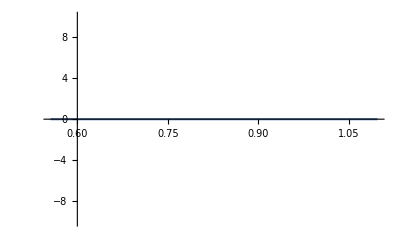

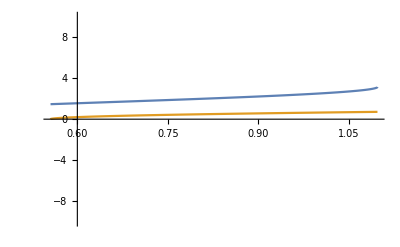

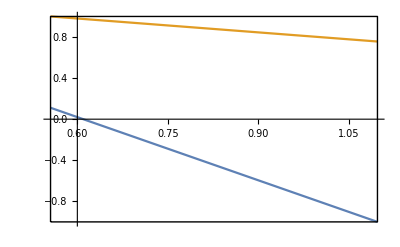

```mathematica
s=.8;
m=1;n=2;

Show[ParametricPlot[{Sin[1/2 ArcCos[(1-(1+s^n)t)/s^(n-m)]+1/2 ArcCos[(1-(1-s^n)t)/s^(n-m)]]^2,Sin[1/2 ArcCos[(1-(1+s^n)t)/s^(n-m)]-1/2 ArcCos[(1-(1-s^n)t)/s^(n-m)]]^2},{t,(1-s^(n-m))/(1-s^n),(1+s^(n-m))/(1+s^n)},PlotRange->{{-0.1,1.1},{-.1,1.1}}],
ParametricPlot[{Sin[1/2 ArcCos[(1-(1+s^n)t)/s^(n-m)]-1/2 ArcCos[(1-(1-s^n)t)/s^(n-m)]]^2,Sin[1/2 ArcCos[(1-(1+s^n)t)/s^(n-m)]+1/2 ArcCos[(1-(1-s^n)t)/s^(n-m)]]^2},{t,(1-s^(n-m))/(1-s^n),(1+s^(n-m))/(1+s^n)},PlotRange->{{-0.1,1.1},{-.1,1.1}}],Graphics[Line[{{0,0},{1,0},{1,1},{0,1},{0,0}}]],Graphics[{Dashed,Line[{{0,0},{1,1}}]}]]



(*Show[ParametricPlot[{Sin[1/2 ArcCos[(1-(1+s^n)t)/s^(n-m)]+1/2 ArcCos[(1-(1-s^n)t)/s^(n-m)]],Sin[1/2 ArcCos[(1-(1+s^n)t)/s^(n-m)]-1/2 ArcCos[(1-(1-s^n)t)/s^(n-m)]]},{t,(1-s^(n-m))/(1-s^n),Min[1/(1-s^n),(1+s^(n-m))/(1+s^n)]},PlotRange->{{-0.1,1.1},{-.1,1.1}}],Graphics[Line[{{0,0},{1,0},{1,1},{0,1},{0,0}}]],Graphics[{Dashed,Line[{{0,0},{1,1}}]}]]*)


Plot[s^m-s^n Cos[1/2 ArcCos[(1-(1+s^n)t)/s^(n-m)]+1/2 ArcCos[(1-(1-s^n)t)/s^(n-m)]]Cos[1/2 ArcCos[(1-(1+s^n)t)/s^(n-m)]-1/2 ArcCos[(1-(1-s^n)t)/s^(n-m)]]-Sin[1/2 ArcCos[(1-(1+s^n)t)/s^(n-m)]+1/2 ArcCos[(1-(1-s^n)t)/s^(n-m)]]Sin[1/2 ArcCos[(1-(1+s^n)t)/s^(n-m)]-1/2 ArcCos[(1-(1-s^n)t)/s^(n-m)]],{t,(1-s^(n-m))/(1-s^n),(1+s^(n-m))/(1+s^n)},PlotRange->{-10,10}]

Plot[{ArcCos[(1-(1+s^n)t)/s^(n-m)],ArcCos[(1-(1-s^n)t)/s^(n-m)]},{t,(1-s^(n-m))/(1-s^n),(1+s^(n-m))/(1+s^n)},PlotRange->{-10,10}]
Show[Plot[{(1-(1+s^n)t)/s^(n-m),(1-(1-s^n)t)/s^(n-m)},{t,(1-s^(n-m))/(1-s^n),(1+s^(n-m))/(1+s^n)},PlotRange->{-1,1}],Graphics[Line[{{(1-s^(n-m))/(1-s^n),-1},{(1+s^(n-m))/(1+s^n),-1},{(1+s^(n-m))/(1+s^n),1},{(1-s^(n-m))/(1-s^n),1},{(1-s^(n-m))/(1-s^n),-1}}]]]

Clear[s,m,n]
```

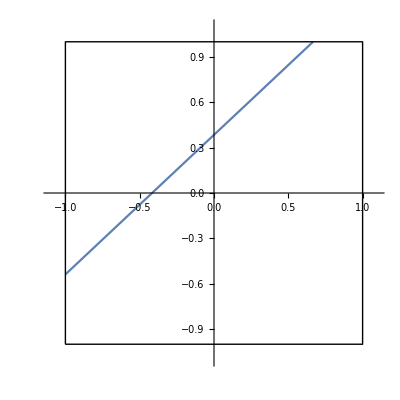

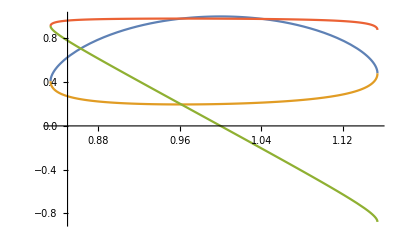

```mathematica
s=.2;
m=1;n=2;

Show[ParametricPlot[{s^(m-n)(1-(1+s^n)t),s^(m-n)(1-(1-s^n)t)},{t,(1-s^(n-m))/(1-s^n),(1+s^(n-m))/(1+s^n)},PlotRange->{{-1.1,1.1},{-1.1,1.1}}],Graphics[Line[{{-1,-1},{1,-1},{1,1},{-1,1},{-1,-1}}]]]

Plot[{Sin[1/2 ArcCos[(1-(1+s^n)t)/s^(n-m)]+1/2 ArcCos[(1-(1-s^n)t)/s^(n-m)]],Sin[1/2 ArcCos[(1-(1+s^n)t)/s^(n-m)]-1/2 ArcCos[(1-(1-s^n)t)/s^(n-m)]],Cos[1/2 ArcCos[(1-(1+s^n)t)/s^(n-m)]+1/2 ArcCos[(1-(1-s^n)t)/s^(n-m)]],Cos[1/2 ArcCos[(1-(1+s^n)t)/s^(n-m)]-1/2 ArcCos[(1-(1-s^n)t)/s^(n-m)]]},{t,(1-s^(n-m))/(1-s^n),(1+s^(n-m))/(1+s^n)},PlotRange->All]
Clear[s,m,n]
```

```mathematica
m=1;n=2;
s=.2;

Show[Table[Show[ParametricPlot[{Sin[1/2 ArcCos[(1-(1+s^n)t)/s^(n-m)]+1/2 ArcCos[(1-(1-s^n)t)/s^(n-m)]]^2,Sin[1/2 ArcCos[(1-(1+s^n)t)/s^(n-m)]-1/2 ArcCos[(1-(1-s^n)t)/s^(n-m)]]^2},{t,(1-s^(n-m))/(1-s^n),Min[1/(1-s^n),(1+s^(n-m))/(1+s^n),1]},PlotRange->{{-0.1,1.1},{-.1,1.1}}],ParametricPlot[{Sin[1/2 ArcCos[(1-(1+s^n)t)/s^(n-m)]-1/2 ArcCos[(1-(1-s^n)t)/s^(n-m)]]^2,Sin[1/2 ArcCos[(1-(1+s^n)t)/s^(n-m)]+1/2 ArcCos[(1-(1-s^n)t)/s^(n-m)]]^2},{t,(1-s^(n-m))/(1-s^n),Min[1/(1-s^n),(1+s^(n-m))/(1+s^n),1]},PlotRange->{{-0.1,1.1},{-.1,1.1}}]],{s,{0.2,0.4,0.6,0.8,.9,.99}}],Graphics[Line[{{0,0},{1,0},{1,1},{0,1},{0,0}}]],Graphics[{Dashed,Line[{{0,0},{1,1}}]}]]


Clear[s,m,n]
```

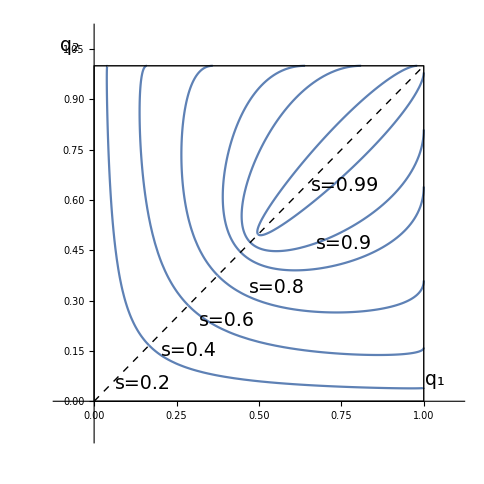

```mathematica
q1=Sin[1/2 ArcCos[(1-(1+s^n)t)/s^(n-m)]+1/2 ArcCos[(1-(1-s^n)t)/s^(n-m)]]^2
q2=Sin[1/2 ArcCos[(1-(1+s^n)t)/s^(n-m)]-1/2 ArcCos[(1-(1-s^n)t)/s^(n-m)]]^2
```

Sin[1/2 ArcCos[s^(m-n) (1-(1-s^n) t)]+1/2 ArcCos[s^(m-n) (1-(1+s^n) t)]]^2

Sin[1/2 ArcCos[s^(m-n) (1-(1-s^n) t)]-1/2 ArcCos[s^(m-n) (1-(1+s^n) t)]]^2

```mathematica
Solve[D[q2,t]==0,t]
```

Solve::nsmet: This system cannot be solved with the methods available to Solve.

Solve[2 (-(s^(m-n) (-1+s^n))/(2 √(1-s^(2 m-2 n) (1-(1-s^n) t)^2))+(s^(m-n) (-1-s^n))/(2 √(1-s^(2 m-2 n) (1-(1+s^n) t)^2))) Cos[1/2 ArcCos[s^(m-n) (1-(1-s^n) t)]-1/2 ArcCos[s^(m-n) (1-(1+s^n) t)]] Sin[1/2 ArcCos[s^(m-n) (1-(1-s^n) t)]-1/2 ArcCos[s^(m-n) (1-(1+s^n) t)]]==0,t]

```mathematica
sq1=(1-(1-s^n)t)/s^(n-m)√(1-((1-(1+s^n)t)/s^(n-m))^2)+(1-(1+s^n)t)/s^(n-m)√(1-((1-(1-s^n)t)/s^(n-m))^2)
sq2=(1-(1-s^n)t)/s^(n-m)√(1-((1-(1+s^n)t)/s^(n-m))^2)-(1-(1+s^n)t)/s^(n-m)√(1-((1-(1-s^n)t)/s^(n-m))^2)
```

s^(m-n) (1-(1+s^n) t) √(1-s^(2 m-2 n) (1-(1-s^n) t)^2)+s^(m-n) (1-(1-s^n) t) √(1-s^(2 m-2 n) (1-(1+s^n) t)^2)

-s^(m-n) (1-(1+s^n) t) √(1-s^(2 m-2 n) (1-(1-s^n) t)^2)+s^(m-n) (1-(1-s^n) t) √(1-s^(2 m-2 n) (1-(1+s^n) t)^2)

```mathematica
D[sq2,t]//FullSimplify
```

s^(m-3 n) (-(s^(2 m) (1+s^n) (-1+t+s^n t) (1+(-1+s^n) t))/(√(1-s^(2 (m-n)) (-1+t+s^n t)^2))+s^(2 n) (-1+s^n) √(1-s^(2 (m-n)) (-1+t+s^n t)^2)-(s^(2 m) (-1+s^n) (-1+t+s^n t) (1+(-1+s^n) t))/(√(1-s^(2 (m-n)) (1+(-1+s^n) t)^2))+s^(2 n) (1+s^n) √(1-s^(2 (m-n)) (1+(-1+s^n) t)^2))

```mathematica
Solve[s^(m-3 n) (-(s^(2 m) (1+s^n) (-1+t+s^n t) (1+(-1+s^n) t))/(√(1-s^(2 (m-n)) (-1+t+s^n t)^2))+s^(2 n) (-1+s^n) √(1-s^(2 (m-n)) (-1+t+s^n t)^2)-(s^(2 m) (-1+s^n) (-1+t+s^n t) (1+(-1+s^n) t))/(√(1-s^(2 (m-n)) (1+(-1+s^n) t)^2))+s^(2 n) (1+s^n) √(1-s^(2 (m-n)) (1+(-1+s^n) t)^2))==0,t]
```

$Aborted

```mathematica
sq1^2+sq2^2//FullSimplify
sq1^2-sq2^2//FullSimplify
```

4 s^(2 m) (s^(-2 n) (-1+t)^2+t^2-s^(2 (m-2 n)) ((-1+t)^2-s^(2 n) t^2)^2)

-4 s^(2 (m-n)) √(1-s^(2 (m-n)) (-1+t+s^n t)^2) √(1-s^(2 (m-n)) (1+(-1+s^n) t)^2) (-1+t (2+(-1+s^(2 n)) t))

```mathematica
D[sq1^2+sq2^2,t]//FullSimplify
```

-8 s^(2 (m-2 n)) (2 s^(2 m) (-1+t)^3+s^(4 n) t (-1+2 s^(2 m) t^2)-s^(2 n) (-1+t) (1+2 s^(2 m) t (-1+2 t)))

```mathematica
Solve[D[sq1^2+sq2^2,t]==0,t]//FullSimplify
```

$Aborted

```mathematica
d1=D[q1,t]//FullSimplify
d2=D[q2,t]//FullSimplify
```

1/2 s^(m-n) ((1+s^n)/(√(1-s^(2 (m-n)) (-1+t+s^n t)^2))-(-1+s^n)/(√(1-s^(2 (m-n)) (1+(-1+s^n) t)^2))) Sin[ArcCos[-s^(m-n) (-1+t+s^n t)]+ArcCos[s^(m-n) (1+(-1+s^n) t)]]

-1/2 s^(m-n) (-(1+s^n)/(√(1-s^(2 (m-n)) (-1+t+s^n t)^2))-(-1+s^n)/(√(1-s^(2 (m-n)) (1+(-1+s^n) t)^2))) Sin[ArcSin[s^(m-n) (-1+t+s^n t)]+ArcSin[s^(m-n) (1+(-1+s^n) t)]]

```mathematica
q1
```

Sin[1/2 ArcCos[s^(m-n) (1-(1-s^n) t)]+1/2 ArcCos[s^(m-n) (1-(1+s^n) t)]]^2

```mathematica
d1 is zero if
```

```mathematica
Solve[ArcCos[-s^(m-n) (-1+t+s^n t)]+ArcCos[s^(m-n) (1+(-1+s^n) t)]==0,t]
```

$Aborted

```mathematica
Solve[{-s^(m-n) (-1+t+s^n t)==1,s^(m-n) (1+(-1+s^n) t)==1},t]
```

{}

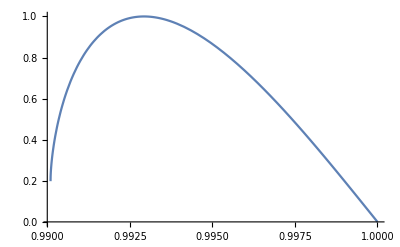

```mathematica
s=.01;
m=1;n=2;
Plot[Sin[ArcCos[-s^(m-n) (-1+t+s^n t)]+ArcCos[s^(m-n) (1+(-1+s^n) t)]],{t,(1-s^(n-m))/(1-s^n),1}]
Clear[n,m,s]
```

```mathematica
Solve[((1+s^n)^2)/(1-s^(2 (m-n)) (-1+t+s^n t)^2)==((-1+s^n)^2)/(1-s^(2 (m-n)) (1+(-1+s^n) t)^2),t]//FullSimplify
```

{{t→(s^(-2 m) (-s^(2 m)+s^(2 n)))/(-1+s^(2 n))}}

```mathematica
(s^(-2 m) (-s^(2 m)+s^(2 n)))/(-1+s^(2 n))/. {m->1,n->2}//FullSimplify
```

```mathematica
sq1/.t->1/(1+s^2)/. {m->1,n->2}//FullSimplify
```

(2 s)/(1+s^2)

```mathematica
d1-d2//Simplify
```

1/2 s^(m-n) (((1+s^n)/(√(1-s^(2 (m-n)) (-1+t+s^n t)^2))-(-1+s^n)/(√(1-s^(2 (m-n)) (1+(-1+s^n) t)^2))) Sin[ArcCos[-s^(m-n) (-1+t+s^n t)]+ArcCos[s^(m-n) (1+(-1+s^n) t)]]+(-(1+s^n)/(√(1-s^(2 (m-n)) (-1+t+s^n t)^2))-(-1+s^n)/(√(1-s^(2 (m-n)) (1+(-1+s^n) t)^2))) Sin[ArcSin[s^(m-n) (-1+t+s^n t)]+ArcSin[s^(m-n) (1+(-1+s^n) t)]])

```mathematica
sq1 sq2//Simplify
s^n √((1-sq1^2)(1- sq2^2))//Simplify
```

-4 s^(2 m-n) (-1+t) t

```mathematica
s^n s^(-2 n) (s^(2 n)-2 s^(2 m) (-1+t)^2-2 s^(2 (m+n)) t^2)//Simplify
```

s^-n (s^(2 n)-2 s^(2 m) (-1+t)^2-2 s^(2 (m+n)) t^2)

```mathematica
-4 s^(2 m-n) (-1+t) t-s^-n (s^(2 n)-2 s^(2 m) (-1+t)^2-2 s^(2 (m+n)) t^2)//FullSimplify
```

-s^n+2 s^(2 m-n) (1+(-1+s^(2 n)) t^2)

```mathematica
s^m-s^n √((1-sq1^2)(1- sq2^2))-sq1 sq2//FullSimplify
```

s^m+4 s^(2 m-n) (-1+t) t-s^n √(s^(-4 n) (s^(2 n)-2 s^(2 m) (1+t (-2+t+s^(2 n) t)))^2)

```mathematica
s^m+4 s^(2 m-n) (-1+t) t-s^n s^(-2 n) (s^(2 n)-2 s^(2 m) (1+t (-2+t+s^(2 n) t)))//FullSimplify
s^m+4 s^(2 m-n) (-1+t) t+s^n s^(-2 n) (s^(2 n)-2 s^(2 m) (1+t (-2+t+s^(2 n) t)))//FullSimplify
```

s^m-s^n+2 s^(2 m-n) (1+t (-4+(3+s^(2 n)) t))

s^m+s^n-2 s^(2 m-n) (1+(-1+s^(2 n)) t^2)

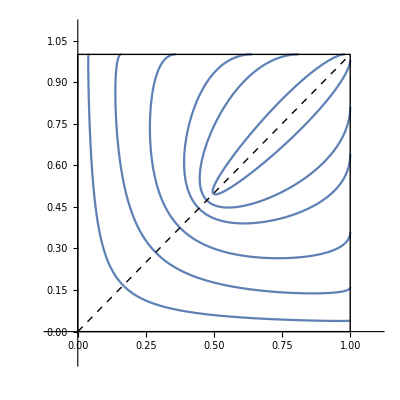

```mathematica
m=1;n=2;
s=.2;

Show[Table[Show[ParametricPlot[{(1-(1-(1+s^n)t)/s^(n-m)(1-(1-s^n)t)/s^(n-m)+√(1-((1-(1+s^n)t)/s^(n-m))^2)√(1-((1-(1-s^n)t)/s^(n-m))^2))/2,(1-(1-(1+s^n)t)/s^(n-m)(1-(1-s^n)t)/s^(n-m)-√(1-((1-(1+s^n)t)/s^(n-m))^2)√(1-((1-(1-s^n)t)/s^(n-m))^2))/2},{t,(1-s^(n-m))/(1-s^n),1},PlotRange->{{-0.1,1.1},{-.1,1.1}}],ParametricPlot[{Sin[1/2 ArcCos[(1-(1+s^n)t)/s^(n-m)]-1/2 ArcCos[(1-(1-s^n)t)/s^(n-m)]]^2,Sin[1/2 ArcCos[(1-(1+s^n)t)/s^(n-m)]+1/2 ArcCos[(1-(1-s^n)t)/s^(n-m)]]^2},{t,(1-s^(n-m))/(1-s^n),1},PlotRange->{{-0.1,1.1},{-.1,1.1}}]],{s,{0.2,0.4,0.6,0.8,.9,.99}}],Graphics[Line[{{0,0},{1,0},{1,1},{0,1},{0,0}}]],Graphics[{Dashed,Line[{{0,0},{1,1}}]}]]


Clear[s,m,n]
```

```mathematica
d2
```

-1/2 s^(m-n) (-(1+s^n)/(√(1-s^(2 (m-n)) (-1+t+s^n t)^2))-(-1+s^n)/(√(1-s^(2 (m-n)) (1+(-1+s^n) t)^2))) Sin[ArcSin[s^(m-n) (-1+t+s^n t)]+ArcSin[s^(m-n) (1+(-1+s^n) t)]]

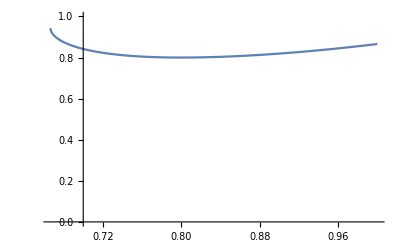

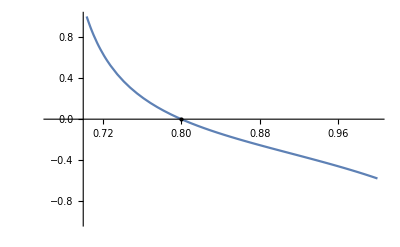

```mathematica
s=.5;
m=1;n=2;
Plot[Sin[ArcSin[s^(m-n) (-1+t+s^n t)]+ArcSin[s^(m-n) (1+(-1+s^n) t)]],{t,(1-s^(n-m))/(1-s^n),1},PlotRange->{0,1}]
Show[Plot[-(1+s^n)/(√(1-s^(2 (m-n)) (-1+t+s^n t)^2))-(-1+s^n)/(√(1-s^(2 (m-n)) (1+(-1+s^n) t)^2)),{t,(1-s^(n-m))/(1-s^n),1},PlotRange->{-1,1}],Graphics[Point[{(1-s^(2 n-2m))/(1-s^(2 n)),0}]]]
Clear[n,m,s]
```

```mathematica
Solve[((1+s^n)^2)/(1-s^(2 (m-n)) (-1+t+s^n t)^2)==((1-s^n)^2)/(1-s^(2 (m-n)) (1+(-1+s^n) t)^2),t]
```

{{t→-(s^(-2 m) (s^(2 m)-s^(2 n)))/(-1+s^(2 n))}}

```mathematica
t=(1-s^(2 n-2m))/(1-s^(2 n))
```

```mathematica
(1+s^n)^2(1-s^(2 (m-n)) (1+(-1+s^n) t)^2)==(1-s^n)^2(1-s^(2 (m-n)) (-1+t+s^n t)^2)
```

```mathematica
(1+s^n)^2(1-s^(2 (m-n)) (1+(-1+s^n) t)^2)//ExpandAll
(1-s^n)^2(1-s^(2 (m-n)) (-1+t+s^n t)^2)//ExpandAll
```

1-s^(2 m)-s^(2 m-2 n)-2 s^(2 m-n)+2 s^n+s^(2 n)-2 s^(2 m) t+2 s^(2 m-2 n) t+2 s^(2 m-n) t-2 s^(2 m+n) t+2 s^(2 m) t^2-s^(2 m-2 n) t^2-s^(2 m+2 n) t^2

1-s^(2 m)-s^(2 m-2 n)+2 s^(2 m-n)-2 s^n+s^(2 n)-2 s^(2 m) t+2 s^(2 m-2 n) t-2 s^(2 m-n) t+2 s^(2 m+n) t+2 s^(2 m) t^2-s^(2 m-2 n) t^2-s^(2 m+2 n) t^2

```mathematica
q2
```

```mathematica
dq2=D[Sin[1/2 ArcCos[s^(m-n) (1-(1-s^n) t)]-1/2 ArcCos[s^(m-n) (1-(1+s^n) t)]],t]
```

(-(s^(m-n) (-1+s^n))/(2 √(1-s^(2 m-2 n) (1-(1-s^n) t)^2))+(s^(m-n) (-1-s^n))/(2 √(1-s^(2 m-2 n) (1-(1+s^n) t)^2))) Cos[1/2 ArcCos[s^(m-n) (1-(1-s^n) t)]-1/2 ArcCos[s^(m-n) (1-(1+s^n) t)]]

```mathematica
D[ArcCos[x],x]
```

-1/(√(1-x^2))

```mathematica
dq2+1/(2 s^(n-m))Cos[1/2 ArcCos[s^(m-n) (1-(1-s^n) t)]-1/2 ArcCos[s^(m-n) (1-(1+s^n) t)]]((1+s^n)/(√(1-((1-(1+s^n)t)/s^(n-m))^2))-(1-s^n)/(√(1-((1-(1-s^n)t)/s^(n-m))^2)))//Simplify
```

0

```mathematica
q2
```

Sin[1/2 ArcCos[s^(m-n) (1-(1-s^n) t)]-1/2 ArcCos[s^(m-n) (1-(1+s^n) t)]]^2

```mathematica
q2/. t->(1-s^(2 n-2m))/(1-s^(2 n))//FullSimplify
```

Sin[1/2 (ArcCsc[(s^m (-1+s^n))/(s^(2 m)-s^n)]-ArcCsc[(s^m (1+s^n))/(s^(2 m)+s^n)])]^2

```mathematica
Sin[1/2 (ArcCsc[(s^m (-1+s^n))/(s^(2 m)-s^n)]-ArcCsc[(s^m (1+s^n))/(s^(2 m)+s^n)])]^2//TrigReduce
```

```mathematica
(1/2 (1-Cos[ArcCsc[(s^m (-1+s^n))/(s^(2 m)-s^n)]-ArcCsc[(s^m (1+s^n))/(s^(2 m)+s^n)]])//TrigToExp)//FullSimplify
```

1/2 (1-√((s^(-2 m) (-1+s^(2 m)) (-s^(2 m)+s^(2 n)))/((-1+s^n)^2)) √((s^(-2 m) (-1+s^(2 m)) (-s^(2 m)+s^(2 n)))/((1+s^n)^2))+(s^(-2 m) (-s^(4 m)+s^(2 n)))/(-1+s^(2 n)))

```mathematica
1/2 (1-(s^(-2 m) (1-s^(2 m)) (s^(2 m)-s^(2 n)))/((1-s^n)^2) +(s^(-2 m) (-s^(4 m)+s^(2 n)))/(-1+s^(2 n)))//FullSimplify
```

(s^(-2 m) (s^m-s^n) (s^(2 m)-s^n) (s^m+s^n))/((-1+s^n)^2 (1+s^n))

```mathematica
(s^(-2 m) (s^m-s^n) (s^(2 m)-s^n) (s^m+s^n))/((-1+s^n)^2 (1+s^n))/. {m->1,n->2}
```

0

```mathematica
(-1+s^n)/(s^m-s^(n-m))(s^m (1+s^n))/(s^(2 m)+s^n)//FullSimplify
((1-((s^m (-1+s^n))/(s^(2 m)-s^n))^2)(1-((s^m (1+s^n))/(s^(2 m)+s^n))^2)//ExpandAll)//Factor
```

(s^(2 m) (-1+s^(2 n)))/(s^(4 m)-s^(2 n))

((-1+s^m)^2 (1+s^m)^2 (s^m-s^n)^2 (s^m+s^n)^2)/((s^(2 m)-s^n)^2 (s^(2 m)+s^n)^2)

```mathematica
1/2(1-(s^(2 m) (-1+s^(2 n)))/(s^(4 m)-s^(2 n))-((1-s^m) (1+s^m) (s^m-s^n) (s^m+s^n))/(s^(4 m)-s^(2 n)))//FullSimplify
```

(s^(4 m)-s^(2 (m+n)))/(s^(4 m)-s^(2 n))

```mathematica
(s^(4 m)-s^(2 (m+n)))/(s^(4 m)-s^(2 n))//Factor
```

(s^(2 m) (s^m-s^n) (s^m+s^n))/((s^(2 m)-s^n) (s^(2 m)+s^n))

```mathematica
q2=Sin[1/2 ArcCos[(1-(1+s^n)t)/s^(n-m)]-1/2 ArcCos[(1-(1-s^n)t)/s^(n-m)]]^2
```

```mathematica
xx=(1-(1+s^n)t)/s^(n-m)/. t-> (1-s^(2n-2m))/(1-s^(2n))//FullSimplify
yy=(1-(1-s^n)t)/s^(n-m)/. t-> (1-s^(2n-2m))/(1-s^(2n))//FullSimplify
```

(s^-m (s^(2 m)-s^n))/(-1+s^n)

(s^-m (s^(2 m)+s^n))/(1+s^n)

```mathematica
(1-xx yy+√((1-xx^2)(1-yy^2)))/2//FullSimplify
```

1/2 (1+√((s^(-4 m) (-1+s^(2 m))^2 (s^(2 m)-s^(2 n))^2)/((-1+s^(2 n))^2))+(s^(-2 m) (-s^(4 m)+s^(2 n)))/(-1+s^(2 n)))

```mathematica
1/2 (1+(s^(-2 m) (1-s^(2 m)) (s^(2 m)-s^(2 n)))/(1-s^(2 n))+(s^(-2 m) (-s^(4 m)+s^(2 n)))/(-1+s^(2 n)))//FullSimplify
```

(s^(-2 m) (-s^(2 m)+s^(2 n)))/(-1+s^(2 n))

```mathematica
q2=(1-s^(2n-2m))/(1-s^(2n))
```

```mathematica
(1-s^(2n-2m))/(1-s^(2n))/. {n->2,m->1}
```

(1-s^2)/(1-s^4)

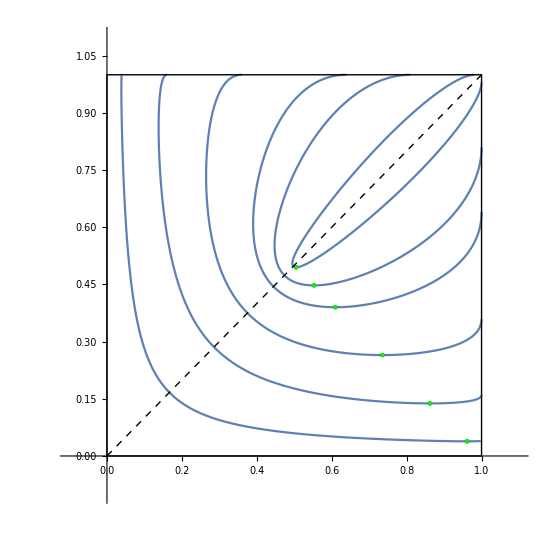

```mathematica
m=1;n=5;
s=.2;

Show[Table[Show[ParametricPlot[{(1-(1-(1+s^n)t)/s^(n-m)(1-(1-s^n)t)/s^(n-m)+√(1-((1-(1+s^n)t)/s^(n-m))^2)√(1-((1-(1-s^n)t)/s^(n-m))^2))/2,(1-(1-(1+s^n)t)/s^(n-m)(1-(1-s^n)t)/s^(n-m)-√(1-((1-(1+s^n)t)/s^(n-m))^2)√(1-((1-(1-s^n)t)/s^(n-m))^2))/2},{t,(1-s^(n-m))/(1-s^n),1},PlotRange->{{-0.1,1.1},{-.1,1.1}}],ParametricPlot[{Sin[1/2 ArcCos[(1-(1+s^n)t)/s^(n-m)]-1/2 ArcCos[(1-(1-s^n)t)/s^(n-m)]]^2,Sin[1/2 ArcCos[(1-(1+s^n)t)/s^(n-m)]+1/2 ArcCos[(1-(1-s^n)t)/s^(n-m)]]^2},{t,(1-s^(n-m))/(1-s^n),1},PlotRange->{{-0.1,1.1},{-.1,1.1}}],Graphics[{PointSize->Large,Point[{(1-(1-(1+s^n)t)/s^(n-m)(1-(1-s^n)t)/s^(n-m)+√(1-((1-(1+s^n)t)/s^(n-m))^2)√(1-((1-(1-s^n)t)/s^(n-m))^2))/2/. t-> (1-s^(2(n-m)))/(1-s^(2n)),(s^(2 m)-s^(2 n))/(1-s^(2 n))}]}],Graphics[{Green,Point[{(1-s^(2 n-2m))/(1-s^(2 n)),(s^(2 m)-s^(2 n))/(1-s^(2 n))}]}]],{s,{0.2,0.4,0.6,0.8,.9,.99}}],Graphics[Line[{{0,0},{1,0},{1,1},{0,1},{0,0}}]],Graphics[{Dashed,Line[{{0,0},{1,1}}]}]]




Clear[s,m,n]
```

```mathematica
(1-(1-(1+s^n)t)/s^(n-m)(1-(1-s^n)t)/s^(n-m)-√((1-((1-(1+s^n)t)/s^(n-m))^2)(1-((1-(1-s^n)t)/s^(n-m))^2)))/2/. t-> (1-s^(2(n-m)))/(1-s^(2n))//FullSimplify
```

1/2 (1-√((s^(-4 m) (-1+s^(2 m))^2 (s^(2 m)-s^(2 n))^2)/((-1+s^(2 n))^2))+(s^(-2 m) (-s^(4 m)+s^(2 n)))/(-1+s^(2 n)))

```mathematica
1/2 (1-(s^(-2 m) (1-s^(2 m)) (s^(2 m)-s^(2 n)))/(1-s^(2 n))+(s^(-2 m) (-s^(4 m)+s^(2 n)))/(-1+s^(2 n)))//FullSimplify
```

(-s^(2 m)+s^(2 n))/(-1+s^(2 n))

```mathematica
(s^(2 m)-s^(2 n))/(1-s^(2 n))
```

```mathematica
(1-(1-(1+s^n)t)/s^(n-m)(1-(1-s^n)t)/s^(n-m)+√((1-((1-(1+s^n)t)/s^(n-m))^2)(1-((1-(1-s^n)t)/s^(n-m))^2)))/2/. t-> (1-s^(2(n-m)))/(1-s^(2n))//FullSimplify
```

1/2 (1+√((s^(-4 m) (-1+s^(2 m))^2 (s^(2 m)-s^(2 n))^2)/((-1+s^(2 n))^2))+(s^(-2 m) (-s^(4 m)+s^(2 n)))/(-1+s^(2 n)))

```mathematica
1/2 (1+(s^(-2 m) (1-s^(2 m)) (s^(2 m)-s^(2 n)))/(1-s^(2 n))+(s^(-2 m) (-s^(4 m)+s^(2 n)))/(-1+s^(2 n)))//FullSimplify
```

(s^(-2 m) (-s^(2 m)+s^(2 n)))/(-1+s^(2 n))

```mathematica
(s^(-2 m) (-s^(2 m)+s^(2 n)))/(-1+s^(2 n))-(1-(s^(2 m)-s^(2 n))/(1-s^(2 n)))//FullSimplify
```

(s^(-2 m) (-s^(4 m)+s^(2 n)))/(-1+s^(2 n))

```mathematica
(1-s^(2 m))/(1-s^(2 n))
```

```mathematica
(1-(1-(1+s^n)t)/s^(n-m)(1-(1-s^n)t)/s^(n-m)+√((1-((1-(1+s^n)t)/s^(n-m))^2)(1-((1-(1-s^n)t)/s^(n-m))^2)))/2/. t-> (1-s^(2(n-m)))/(1-s^(2n))//FullSimplify
```

1/2 (1+√((s^(-4 m) (-1+s^(2 m))^2 (s^(2 m)-s^(2 n))^2)/((-1+s^(2 n))^2))+(s^(-2 m) (-s^(4 m)+s^(2 n)))/(-1+s^(2 n)))

```mathematica
1/2 (1+(s^(-2 m) (1-s^(2 m)) (s^(2 m)-s^(2 n)))/(1-s^(2 n))+(s^(-2 m) (-s^(4 m)+s^(2 n)))/(-1+s^(2 n)))//FullSimplify
```

(s^(-2 m) (-s^(2 m)+s^(2 n)))/(-1+s^(2 n))

```mathematica
(1-(1-(1+s^n)t)/s^(n-m)(1-(1-s^n)t)/s^(n-m)-√((1-((1-(1+s^n)t)/s^(n-m))^2)(1-((1-(1-s^n)t)/s^(n-m))^2)))/2/. t-> (1-s^(n-m))/(1-s^n)//FullSimplify
```

(-s^m+s^n)/(-1+s^n)

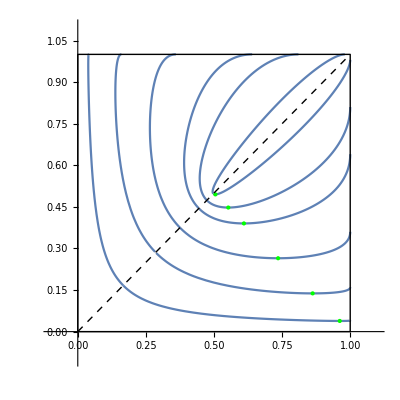

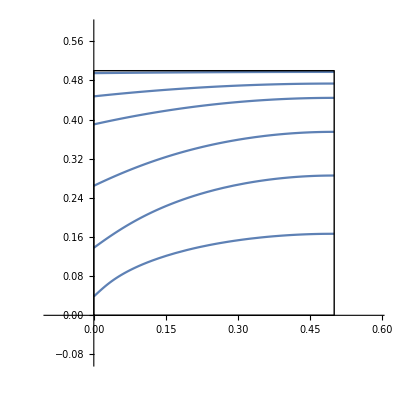

```mathematica
m=1;n=2;
s=.2;

x=(1-(1+s^n)t)/s^(n-m);
y=(1-(1-s^n)t)/s^(n-m);

Show[Table[x=(1-(1+s^n)t)/s^(n-m);y=(1-(1-s^n)t)/s^(n-m);q1=(1-x y+√(1-x^2)√(1-y^2))/2;q2=(1-x y-√(1-x^2)√(1-y^2))/2;Show[ParametricPlot[{q1,q2},{t,(1-s^(n-m))/(1-s^n),1},PlotRange->{{-0.1,1.1},{-.1,1.1}}],ParametricPlot[{q2,q1},{t,(1-s^(n-m))/(1-s^n),1},PlotRange->{{-0.1,1.1},{-.1,1.1}}],Graphics[{Green,Point[{(1-s^(2 n-2m))/(1-s^(2 n)),(s^(2 m)-s^(2 n))/(1-s^(2 n))}]}]],{s,{0.2,0.4,0.6,0.8,.9,.99}}],Graphics[Line[{{0,0},{1,0},{1,1},{0,1},{0,0}}]],Graphics[{Dashed,Line[{{0,0},{1,1}}]}]]

(**********************************************************************************************************************************)

(*Show[Table[x=(1-(1+s^n)t)/s^(n-m);y=(1-(1-s^n)t)/s^(n-m);q1=(1-x y+√(1-x^2)√(1-y^2))/2;q2=(1-x y-√(1-x^2)√(1-y^2))/2;
dq1=(√(q1(1-q1)))/s^(n-m)((1+s^n)/(√(1-x^2))+(1-s^n)/(√(1-y^2)));dq2=(√(q2(1-q2)))/s^(n-m)((1+s^n)/(√(1-x^2))-(1-s^n)/(√(1-y^2)));ParametricPlot[{dq2/(dq2-dq1),dq2/(dq2-dq1)q1+dq1/(dq1-dq2)q2},{t,(1-s^(n-m))/(1-s^n)+10^-10,(1-s^(2 n-2m))/(1-s^(2 n))},PlotRange->{{-0.1,.6},{-.1,.6}}],{s,{0.2,0.4,0.6,0.8,.9,.99}}]]*)


Uf=Show[Table[x=(1-(1+s^n)t)/s^(n-m);y=(1-(1-s^n)t)/s^(n-m);q1=(1-x y+√(1-x^2)√(1-y^2))/2;q2=(1-x y-√(1-x^2)√(1-y^2))/2;
dq1=(√(q1(1-q1)))/s^(n-m)((1+s^n)/(√(1-x^2))+(1-s^n)/(√(1-y^2)));dq2=(√(q2(1-q2)))/s^(n-m)((1+s^n)/(√(1-x^2))-(1-s^n)/(√(1-y^2)));ParametricPlot[{dq2/(dq2-dq1),dq2/(dq2-dq1)q1+dq1/(dq1-dq2)q2},{t,(1-s^(n-m))/(1-s^n)+10^-10,(1-s^(2 n-2m))/(1-s^(2 n))},PlotRange->{{-0.09,.59},{-.09,.59}}],{s,{0.2,0.4,0.6,0.8,.9,.99}}],Graphics[Line[{{0,0},{1/2,0},{1/2,1/2},{0,1/2},{0,0}}]]]




Clear[s,m,n]
```

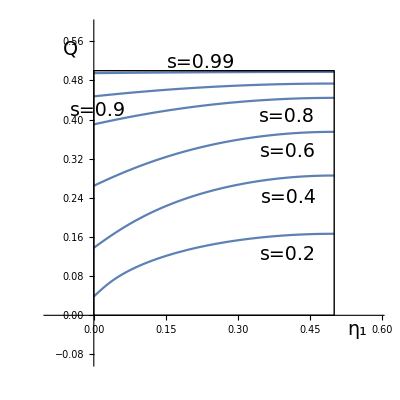

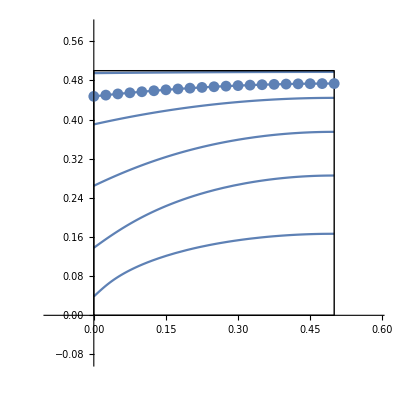

```mathematica
η2=1-η1;
s=.9;
m=1;n=2;
ja=ListPlot[Table[ma=Minimize[{η1 Sin[θ1]^2+η2 Sin[θ2]^2,s^m==s^n Cos[θ1]Cos[θ2]+Sin[θ1]Sin[θ2]},{θ1,θ2}];{η1,ma[[1]]},{η1,0,1/2,1/40}],PlotRange->{{0,1/2},{0,1/2}}];
Show[Uf,ja]

Clear[η2,s,m,n]
```

```mathematica
QO[x_,S_]:=If[x< S^2/(1+S^2),(1-x) S^2+x,0]+If[x> 1/(1+S^2),x S^2+(1-x),0]+If[ S^2/(1+S^2)≤x≤  1/(1+S^2),2 √(x(1-x))S,0]
```

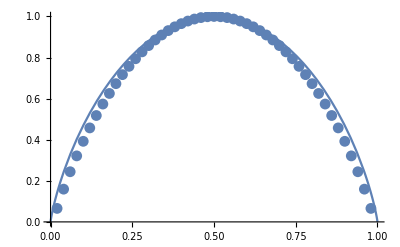

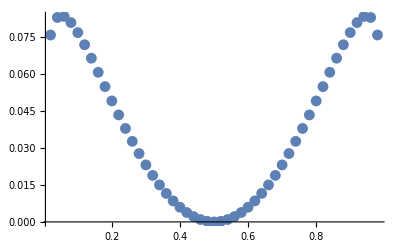

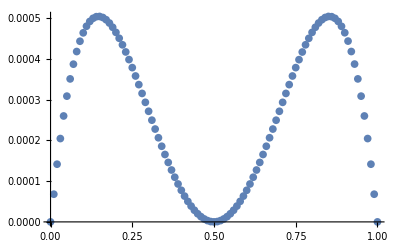

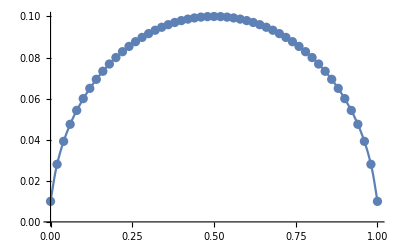

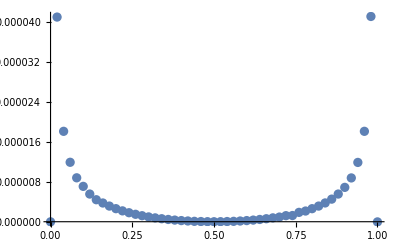

```mathematica
η2=1-η1;
s=.1;
m=1;n=2;
ja=ListPlot[Table[ma=Minimize[{η1 Sin[θ1]^2+η2 Sin[θ2]^2,s^m==s^n Cos[θ1]Cos[θ2]+Sin[θ1]Sin[θ2]},{θ1,θ2}];{η1,-(η1 Cos[θ1]^2)/(η1 Cos[θ1]^2+η2 Cos[θ2]^2)Log[2,(η1 Cos[θ1]^2)/(η1 Cos[θ1]^2+η2 Cos[θ2]^2)]-(η2 Cos[θ2]^2)/(η1 Cos[θ1]^2+η2 Cos[θ2]^2)Log[2,(η2 Cos[θ2]^2)/(η1 Cos[θ1]^2+η2 Cos[θ2]^2)]/. ma[[2]]},{η1,0,1,.02}],PlotRange->All];
sh=Plot[-η1 Log[2,η1]-η2 Log[2,η2],{η1,0,1}];
Show[sh,ja]
InfGainG=ListPlot[Table[ma=Minimize[{η1 Sin[θ1]^2+η2 Sin[θ2]^2,s^m==s^n Cos[θ1]Cos[θ2]+Sin[θ1]Sin[θ2]},{θ1,θ2}];{η1,-η1 Log[2,η1]-η2 Log[2,η2]-(-(η1 Cos[θ1]^2)/(η1 Cos[θ1]^2+η2 Cos[θ2]^2)Log[2,(η1 Cos[θ1]^2)/(η1 Cos[θ1]^2+η2 Cos[θ2]^2)]-(η2 Cos[θ2]^2)/(η1 Cos[θ1]^2+η2 Cos[θ2]^2)Log[2,(η2 Cos[θ2]^2)/(η1 Cos[θ1]^2+η2 Cos[θ2]^2)]/. ma[[2]])},{η1,0,1,.02}],PlotRange->All]

ListPlot[Table[ma=Minimize[{η1 Sin[θ1]^2+η2 Sin[θ2]^2,s^m==s^n Cos[θ1]Cos[θ2]+Sin[θ1]Sin[θ2]},{θ1,θ2}];{η1,(η1 η2)^2(Sin[θ1]^2-Sin[θ2]^2)^2 /. ma[[2]]},{η1,0,1,.01}],PlotRange->All]

v1=ListPlot[Table[ma=Minimize[{η1 Sin[θ1]^2+η2 Sin[θ2]^2,s^m==s^n Cos[θ1]Cos[θ2]+Sin[θ1]Sin[θ2]},{θ1,θ2}];{η1,η1 Sin[θ1]^2+η2 Sin[θ2]^2 +(η1 Cos[θ1]^2+η2 Cos[θ2]^2)QO[(η1 Cos[θ1]^2)/(η1 Cos[θ1]^2+η2 Cos[θ2]^2),s^n]/. ma[[2]]},{η1,0,1,.02}],PlotRange->All];
v2=Plot[ QO[η1,s^m],{η1,0,1}];
Show[v1,v2]

SubOptG=ListPlot[Table[ma=Minimize[{η1 Sin[θ1]^2+η2 Sin[θ2]^2,s^m==s^n Cos[θ1]Cos[θ2]+Sin[θ1]Sin[θ2]},{θ1,θ2}];{η1,(η1 Sin[θ1]^2+η2 Sin[θ2]^2 +(η1 Cos[θ1]^2+η2 Cos[θ2]^2)QO[(η1 Cos[θ1]^2)/(η1 Cos[θ1]^2+η2 Cos[θ2]^2),s^n]/. ma[[2]])-QO[η1,s^m]},{η1,0,1,.02}],PlotRange->All]

Clear[η2,s,m,n]
```

```mathematica
QO[x_,S_]:=If[x< S^2/(1+S^2),(1-x) S^2+x,0]+If[x> 1/(1+S^2),x S^2+(1-x),0]+If[ S^2/(1+S^2)≤x≤  1/(1+S^2),2 √(x(1-x))S,0]
H2[x_]:=-x Log[2,x]-(1-x)Log[2,1-x]
```

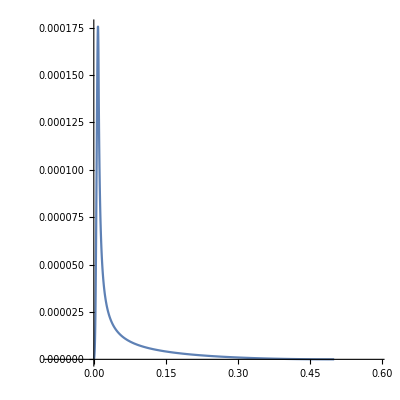

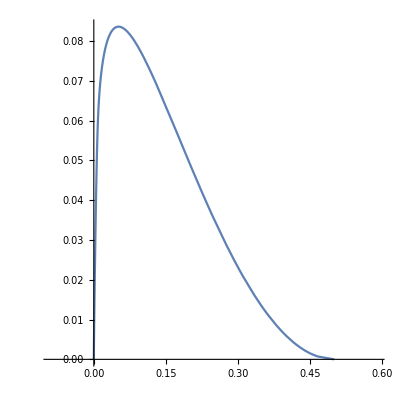

```mathematica
m=1;n=2;
s=.1;


x=(1-(1+s^n)t)/s^(n-m);y=(1-(1-s^n)t)/s^(n-m);q1=(1-x y+√(1-x^2)√(1-y^2))/2;q2=(1-x y-√(1-x^2)√(1-y^2))/2;
dq1=(√(q1(1-q1)))/s^(n-m)((1+s^n)/(√(1-x^2))+(1-s^n)/(√(1-y^2)));dq2=(√(q2(1-q2)))/s^(n-m)((1+s^n)/(√(1-x^2))-(1-s^n)/(√(1-y^2)));

SubOptGAn=ParametricPlot[{dq2/(dq2-dq1),dq2/(dq2-dq1)q1+dq1/(dq1-dq2)q2+(1-dq2/(dq2-dq1)q1-dq1/(dq1-dq2)q2)QO[(dq2/(dq2-dq1)(1-q1))/(1-dq2/(dq2-dq1)q1-dq1/(dq1-dq2)q2),s^n]-QO[dq2/(dq2-dq1),s^m]},{t,(1-s^(n-m))/(1-s^n),(1-s^(2 n-2m))/(1-s^(2 n))},PlotRange->{{-0.09,.59},All},AspectRatio->1]
InfGainGAn=ParametricPlot[{dq2/(dq2-dq1),H2[dq2/(dq2-dq1)]-H2[(dq2/(dq2-dq1)(1-q1))/(1-dq2/(dq2-dq1)q1-dq1/(dq1-dq2)q2)]},{t,(1-s^(n-m))/(1-s^n),(1-s^(2 n-2m))/(1-s^(2 n))},PlotRange->{{-0.09,.59},All},AspectRatio->1]






Clear[s,m,n,x,y,q1,q2,dq1,dq2]
```

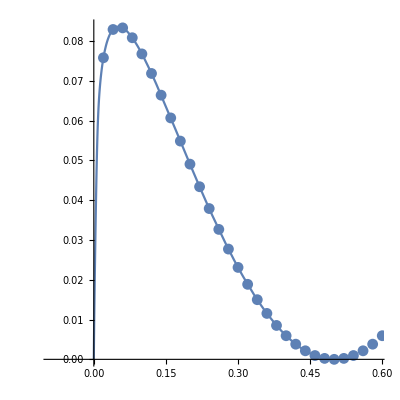

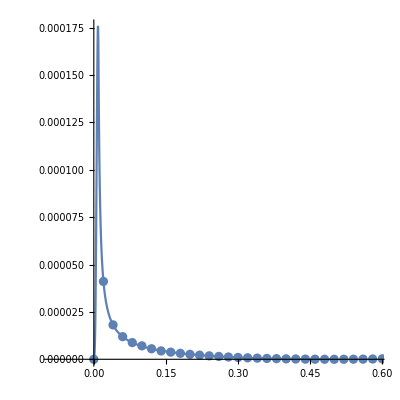

```mathematica
Show[InfGainGAn,InfGainG]
Show[SubOptGAn,SubOptG]
```

```mathematica
x=(1-(1+s^n)t)/s^(n-m);
y=(1-(1-s^n)t)/s^(n-m);

x=(1-(1+s^n)t)/s^(n-m);y=(1-(1-s^n)t)/s^(n-m);q1=(1-x y+√(1-x^2)√(1-y^2))/2;q2=(1-x y-√(1-x^2)√(1-y^2))/2
```

1/2 (1-s^(2 m-2 n) (1-(1-s^n) t) (1-(1+s^n) t)-√(1-s^(2 m-2 n) (1-(1-s^n) t)^2) √(1-s^(2 m-2 n) (1-(1+s^n) t)^2))

```mathematica
FullSimplify[q2/. t-> (1-s^(2(n-m)))/(1-s^(2n))//FullSimplify,{1>s>0,n>m>1}]/. {Sign[1-s^n]->1,Sign[-1+s^n]->-1}
```

-(s^(2 m)-s^(2 n))/(-1+s^(2 n))

```mathematica
sp=.5;
bb=Minimize[sp Abs[Cos[θ1]Cos[θ2]]+Abs[Sin[θ1]Sin[θ2]],{θ1,θ2}]
{Cos[θ1]^2,Cos[θ2]^2}/. bb[[2]]
```

{2.90373×10^-10,{θ1→1.5708,θ2→-2.71317×10^-11}}

{2.77184×10^-19,1.}

{4.39098×10^-18,1.}

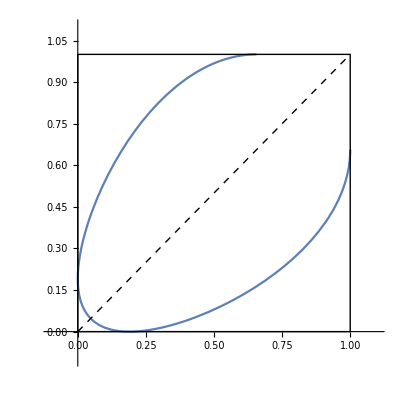

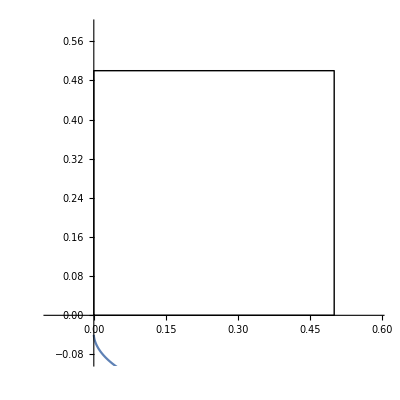

```mathematica
m=2;n=1;
s=.7;

x=(1-(1+s^n)t)/s^(n-m);
y=(1-(1-s^n)t)/s^(n-m);

Show[Table[x=(1-(1+s^n)t)/s^(n-m);y=(1-(1-s^n)t)/s^(n-m);q1=(1-x y+√(1-x^2)√(1-y^2))/2;q2=(1-x y-√(1-x^2)√(1-y^2))/2;Show[ParametricPlot[{q1,q2},{t,(1-s^(n-m))/(1-s^n),1},PlotRange->{{-0.1,1.1},{-.1,1.1}}],ParametricPlot[{q2,q1},{t,(1-s^(n-m))/(1-s^n),1},PlotRange->{{-0.1,1.1},{-.1,1.1}}],Graphics[{Green,Point[{(1-s^(2 n-2m))/(1-s^(2 n)),(s^(2 m)-s^(2 n))/(1-s^(2 n))}]}]],{s,{0.9}}],Graphics[Line[{{0,0},{1,0},{1,1},{0,1},{0,0}}]],Graphics[{Dashed,Line[{{0,0},{1,1}}]}]]


Clear[s,m,n]
```

```mathematica
Clear[s,sp]
```

```mathematica
x=(1-(1+sp)t)/(sp/s);
y=(1-(1-sp)t)/(sp/s);

q1=(1-x y+√((1-x^2)(1-y^2)))/2;q2=(1-x y-√((1-x^2)(1-y^2)))/2;
```

```mathematica
q1
```

1/2 (1-(s^2 (1-(1-sp) t) (1-(1+sp) t))/sp^2+√(1-(s^2 (1-(1-sp) t)^2)/sp^2) √(1-(s^2 (1-(1+sp) t)^2)/sp^2))

```mathematica
√((1-q1)(1-q2))sp+√(q1 q2)//FullSimplify
```

sp √((s^2 (-1+t)^2)/sp^2)+√(s^2 t^2)

```mathematica
FullSimplify[√((1-q1)(1-q2))sp+√(q1 q2)//FullSimplify,{s>0,sp<0,t>1}]
```

s

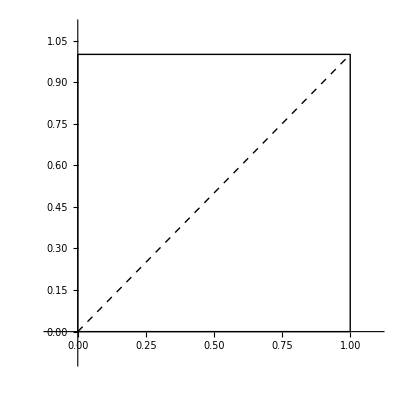

```mathematica
m=2;n=1;
s=.7;



Show[Table[x=(1-(1+sp)t)/(sp/s);
y=(1-(1-sp)t)/(sp/s);

q1=(1-x y+√((1-x^2)(1-y^2)))/2;q2=(1-x y-√((1-x^2)(1-y^2)))/2;Show[ParametricPlot[{q1,q2},{t,1,2},PlotRange->{{-0.1,1.1},{-.1,1.1}}],ParametricPlot[{q2,q1},{t,(1-s^(n-m))/(1-s^n),1},PlotRange->{{-0.1,1.1},{-.1,1.1}}],Graphics[{Green,Point[{(1-s^(2 n-2m))/(1-s^(2 n)),(s^(2 m)-s^(2 n))/(1-s^(2 n))}]}]],{s,{0.5}}],Graphics[Line[{{0,0},{1,0},{1,1},{0,1},{0,0}}]],Graphics[{Dashed,Line[{{0,0},{1,1}}]}]]
```

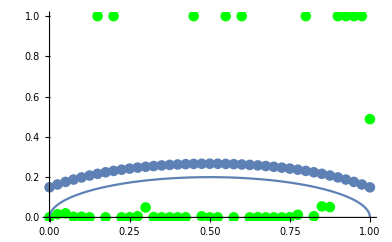

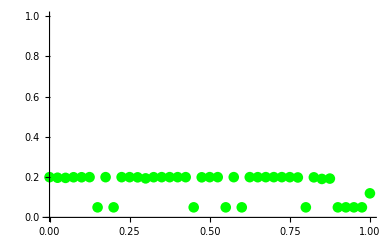

```mathematica
η2=1-η1;
s=.45;
sp=.25;
ϕ=.4;
ja=ListPlot[Table[ma=NMinimize[{η1 Sin[θ1]^2+η2 Sin[θ2]^2,s== sp Cos[θ1]Cos[θ2]+ϕ Sin[θ1]Sin[θ2],0≤ θ1≤ π/2,0≤ θ2≤ π/2},{θ1,θ2}];{η1,ma[[1]]},{η1,0,1,1/40}],PlotRange->{{0,1},{0,1}},PlotStyle-> Green];
jaa=ListPlot[Table[ma=NMinimize[{η1 Sin[θ1]^2+η2 Sin[θ2]^2,s==sp Cos[θ1]Cos[θ2]+Sin[θ1]Sin[θ2],0≤ θ1≤ π/2,0≤ θ2≤ π/2},{θ1,θ2}];{η1,ma[[1]]},{η1,0,1,1/40}],PlotRange->{{0,1},{0,1}}];
pj=Plot[2(s-sp)/1 √(η1 η2),{η1,0,1}];
Show[jaa,ja,pj]

ListPlot[Table[ma=NMinimize[{η1 Sin[θ1]^2+η2 Sin[θ2]^2,s== sp Cos[θ1]Cos[θ2]+ϕ Sin[θ1]Sin[θ2],0≤ θ1≤ π/2,0≤ θ2≤ π/2},{θ1,θ2}];{η1,Abs[sp Cos[θ1]Cos[θ2]+ϕ Sin[θ1]Sin[θ2]-s]/.ma[[2]]},{η1,0,1,1/40}],PlotRange->{{0,1},{0,1}},PlotStyle-> Green]

Clear[η2,s,m,n]
```

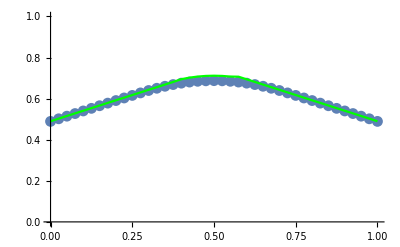

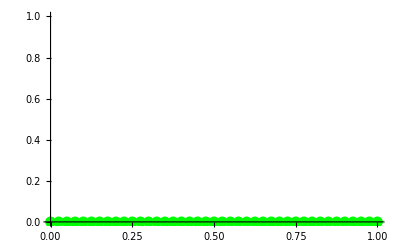

```mathematica
η2=1-η1;
s=.7;
sp=.4;
ϕ=1.;
α=.1;
ja=ListPlot[Table[ma=NMinimize[{η1 Sin[θ1]^2+η2 Sin[θ2]^2,s==-α sp Cos[θ1]Cos[θ2]+ϕ Sin[θ1]Sin[θ2],0≤ θ1≤ π/2,0≤ θ2≤ π/2},{θ1,θ2}];{η1,ma[[1]]},{η1,0,1,1/40}],PlotRange->{{0,1},{0,1}},PlotStyle-> Green,Joined->True];
jaa=ListPlot[Table[ma=NMinimize[{η1 Sin[θ1]^2+η2 Sin[θ2]^2,s==α sp Cos[θ1]Cos[θ2]+ϕ Sin[θ1]Sin[θ2],0≤ θ1≤ π/2,0≤ θ2≤ π/2},{θ1,θ2}];{η1,ma[[1]]},{η1,0,1,1/40}],PlotRange->{{0,1},{0,1}}];
(*pj=Plot[2(s-sp)/1 √(η1 η2),{η1,0,1}];*)
Show[jaa,ja]

ListPlot[Table[ma=NMinimize[{η1 Sin[θ1]^2+η2 Sin[θ2]^2,s==α sp Cos[θ1]Cos[θ2]+ϕ Sin[θ1]Sin[θ2],0≤ θ1≤ π/2,0≤ θ2≤ π/2},{θ1,θ2}];{η1,Abs[α sp Cos[θ1]Cos[θ2]+ϕ Sin[θ1]Sin[θ2]-s]/.ma[[2]]},{η1,0,1,1/40}],PlotRange->{{0,1},{0,1}},PlotStyle-> Green]

Clear[η2,s,m,n]
```

{1.10119,1}

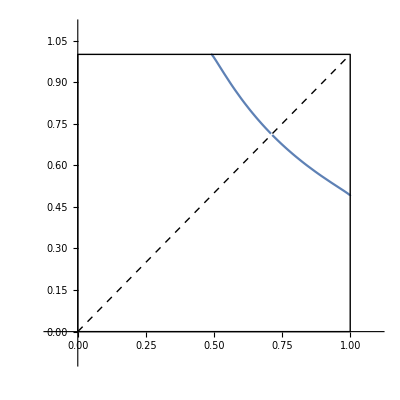

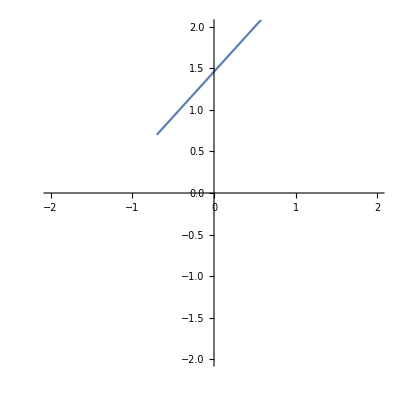

{1.10119,1}

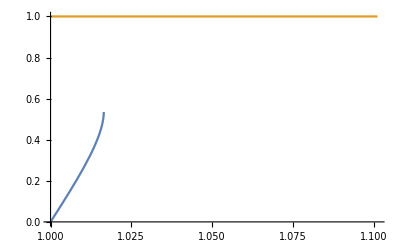

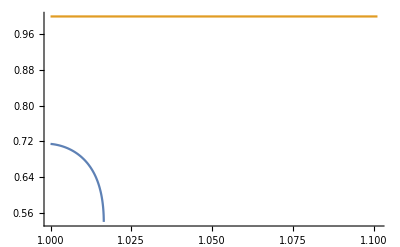

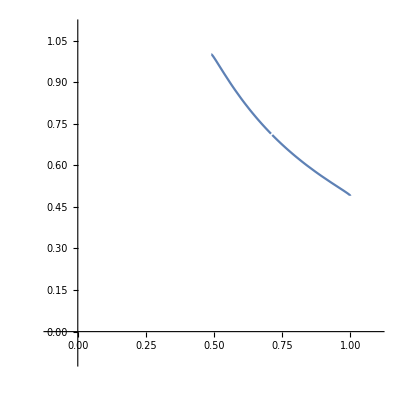

```mathematica
α=-.3;
ϕ=1;







s=.7;
sp=.4;
α=-.1;
ϕ=1;
x=(1-(ϕ+α sp)t)/(α sp/s);
y=(1-(ϕ-α sp)t)/(α sp/s);q1=(1-x y+√(1-x^2)√(1-y^2))/2;q2=(1-x y-√(1-x^2)√(1-y^2))/2;
{(1+Abs[α] sp/s)/(ϕ-Abs[α] sp),1/ϕ}
Show[ParametricPlot[{q1,q2},{t,(1+Abs[α] sp/s)/(ϕ-Abs[α] sp),1/ϕ},PlotRange->{{-0.1,1.1},{-.1,1.1}}],ParametricPlot[{q2,q1},{t,(1+Abs[α] sp/s)/(ϕ-Abs[α] sp),1/ϕ},PlotRange->{{-0.1,1.1},{-.1,1.1}}],Graphics[Line[{{0,0},{1,0},{1,1},{0,1},{0,0}}]],Graphics[{Dashed,Line[{{0,0},{1,1}}]}]
]

ParametricPlot[{x,y}//Chop,{t,1/ϕ,(1+Abs[α] sp/s)/(ϕ-Abs[α] sp)},PlotRange->{{-2,2},{-2,2}}]
{(1+Abs[α] sp/s)/(ϕ-Abs[α] sp),1/ϕ}

(*Plot[Cos[1/2 ArcCos[(1-(1+s^2)t)/s]+1/2 ArcCos[(1-(1-s^2)t)/s]],{t,1,2}]*)
Plot[{Cos[1/2 ArcCos[x]+1/2 ArcCos[y]],1},{t,1/ϕ,(1+Abs[α] sp/s)/(ϕ-Abs[α] sp)}]
Plot[{Cos[1/2 ArcCos[x]-1/2 ArcCos[y]],1},{t,1/ϕ,(1+Abs[α] sp/s)/(ϕ-Abs[α] sp)}]
Show[ParametricPlot[{Sin[1/2 ArcCos[x]+1/2 ArcCos[y]]^2,Sin[1/2 ArcCos[x]-1/2 ArcCos[y]]^2},{t,1/ϕ,(1+Abs[α] sp/s)/(ϕ-Abs[α] sp)},PlotRange->{{-0.1,1.1},{-.1,1.1}}],
ParametricPlot[{Sin[1/2 ArcCos[x]-1/2 ArcCos[y]]^2,Sin[1/2 ArcCos[x]+1/2 ArcCos[y]]^2},{t,1/ϕ,(1+Abs[α] sp/s)/(ϕ-Abs[α] sp)},PlotRange->{{-0.1,1.1},{-.1,1.1}}]]

Clear[s,m,n]
```

{0.714286,1}

{1,2.61905}

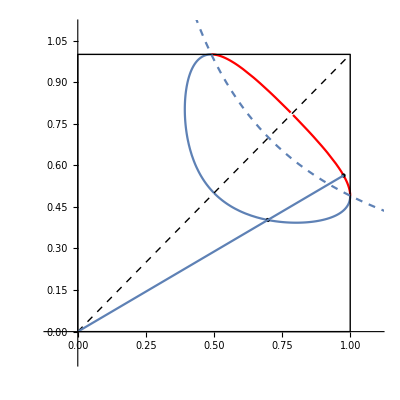

```mathematica
s=.7;
sp=.5;
α=.8;
ϕ=1;
β=π/6;
x=(1-(ϕ+α sp)t)/(α sp/s);
y=(1-(ϕ-α sp)t)/(α sp/s);q1=(1-x y+√(1-x^2)√(1-y^2))/2;q2=(1-x y-√(1-x^2)√(1-y^2))/2;
{(1-α sp/s)/(ϕ-α sp),1/ϕ}
out=Show[ParametricPlot[{q1,q2},{t,(1-α sp/s)/(ϕ-α  sp),1/ϕ},PlotRange->{{-0.1,1.1},{-.1,1.1}}],ParametricPlot[{q2,q1},{t,(1-α sp/s)/(ϕ-α sp),1/ϕ},PlotRange->{{-0.1,1.1},{-.1,1.1}}],Graphics[Line[{{0,0},{1,0},{1,1},{0,1},{0,0}}]],Graphics[{Dashed,Line[{{0,0},{1,1}}]}]
];

x=(1-(ϕ-α sp)t)/(-α sp/s);
y=(1-(ϕ+α sp)t)/(-α sp/s);q1=(1-x y+√(1-x^2)√(1-y^2))/2;q2=(1-x y-√(1-x^2)√(1-y^2))/2;
{1/ϕ,(1+α sp/s)/(ϕ-α sp)}

in=Show[ParametricPlot[{q1,q2},{t,1/ϕ,(1+α sp/s)/(ϕ-α sp)},PlotRange->{{-0.1,1.1},{-.1,1.1}},PlotStyle-> Red],ParametricPlot[{q2,q1},{t,1/ϕ,(1+α sp/s)/(ϕ-α sp)},PlotRange->{{-0.1,1.1},{-.1,1.1}},PlotStyle-> Red]];
SUS={t->(Csc[β] Sec[β] (-2 s ϕ √(Cos[β] Sin[β])+sp^2 α^2 (Cos[β]+Sin[β])-sp α √(sp^2 α^2-4 s ϕ √(Cos[β] Sin[β]) (Cos[β]+Sin[β])+(2 s^2-sp^2 α^2+2 ϕ^2) Sin[2 β])))/(2 (sp α-ϕ) (sp α+ϕ)),t->(-2 s ϕ √(Csc[β] Sec[β])+sp α Csc[β] Sec[β] (sp α (Cos[β]+Sin[β])+√(sp^2 α^2-4 s ϕ √(Cos[β] Sin[β]) (Cos[β]+Sin[β])+(2 s^2-sp^2 α^2+2 ϕ^2) Sin[2 β])))/(2 (sp α-ϕ) (sp α+ϕ))};

Clear[t]
ppp1=Graphics[{Black,PointSize->Medium,Point[{Cos[β]t,Sin[β]t}/. SUS[[1]]]}];
ppp2=Graphics[{Black,PointSize->Medium,Point[{Cos[β]t,Sin[β]t}/. SUS[[2]]]}];
lll=ParametricPlot[{Cos[β]t,Sin[β]t},{t,0,Max[t/. SUS[[1]],t/. SUS[[2]]]}];
asy=ParametricPlot[{√(Cos[β]/Sin[β])s,√(Sin[β]/Cos[β])s},{β,0,π/2},PlotStyle-> Dashed];


SA1=Show[in,out,ppp1,ppp2,lll,asy]
```

```mathematica
Clear[s,sp,α,ϕ,β]
```

```mathematica
sss=FullSimplify[Solve[(s+sp α √((1- Cos[β] t)(1-Sin[β] t)))/ϕ==√(Sin[β] Cos[β]) t,t]//FullSimplify,{0<β<π/2,1>s>0,s>sp>0,0<α<1,1>ϕ>s}]
```

{{t→(Csc[β] Sec[β] (-2 s ϕ √(Cos[β] Sin[β])+sp^2 α^2 (Cos[β]+Sin[β])-sp α √(sp^2 α^2-4 s ϕ √(Cos[β] Sin[β]) (Cos[β]+Sin[β])+(2 s^2-sp^2 α^2+2 ϕ^2) Sin[2 β])))/(2 (sp α-ϕ) (sp α+ϕ))},{t→(-2 s ϕ √(Csc[β] Sec[β])+sp α Csc[β] Sec[β] (sp α (Cos[β]+Sin[β])+√(sp^2 α^2-4 s ϕ √(Cos[β] Sin[β]) (Cos[β]+Sin[β])+(2 s^2-sp^2 α^2+2 ϕ^2) Sin[2 β])))/(2 (sp α-ϕ) (sp α+ϕ))}}

```mathematica
t/. sss//FullSimplify
```

{-(2 (s-sp α))/(√2 sp α-ϕ),(2 (s+sp α))/(√2 sp α+ϕ)}

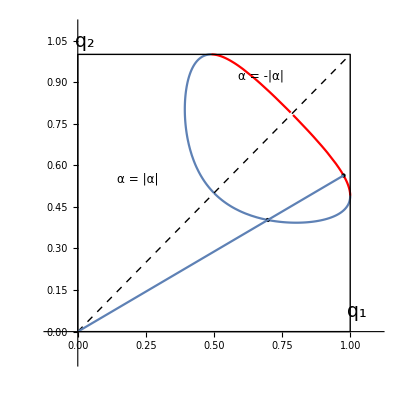

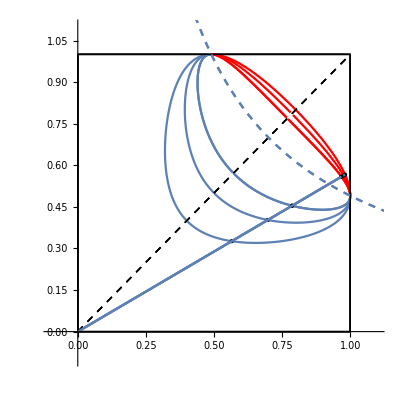

```mathematica
Show[SA8,SA6,SA10,SA1,asy]
```

```mathematica
Show[SA8,asy]
```

-Graphics-

```mathematica
Clear[ϕ]
```

```mathematica
ff=σ √(1-ξ1 t)√(1-ξ2 t)+ϕ √(ξ1 ξ2)t
```

√(1-t ξ1) √(1-t ξ2) σ+t √(ξ1 ξ2) ϕ

```mathematica
D[ff,σ]
```

√(1-t ξ1) √(1-t ξ2)

```mathematica
D[ff,t]//Together
```

(-ξ1 σ-ξ2 σ+2 t ξ1 ξ2 σ+2 √(1-t ξ1) √(ξ1 ξ2) √(1-t ξ2) ϕ)/(2 √(1-t ξ1) √(1-t ξ2))

```mathematica
(-ξ1 σ-ξ2 σ+2 t ξ1 ξ2 σ+2 √(1-t ξ1) √(ξ1 ξ2) √(1-t ξ2) ϕ)/(2 √(1-t ξ1) √(1-t ξ2))
```

```mathematica
-D[ff,σ]/D[ff,t]//FullSimplify
```

-(2 (-1+t ξ1) (-1+t ξ2))/(-ξ2 σ+ξ1 (-1+2 t ξ2) σ+2 √(1-t ξ1) √(ξ1 ξ2) √(1-t ξ2) ϕ)

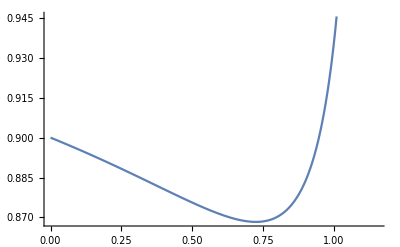

```mathematica
s=.9;
σ=.8;
ϕ=1;
ñ=π/3;
ξ1=Cos[ñ];
ξ2=Sin[ñ];
Plot[(s-ϕ √(ξ1 ξ2) t)/(√(1-t ξ1)  √(1-t ξ2) ϕ),{t,0,Min[1/ξ1,1/ξ2,s/(ϕ √(ξ1 ξ2))]}]

Clear[ϕ,σ,ξ1,ξ2,ñ,s]
```

```mathematica
-(2 (-1+t ξ1) (-1+t ξ2))/(-ξ2 σ+ξ1 (-1+2 t ξ2) σ+2 √(1-t ξ1) √(ξ1 ξ2) √(1-t ξ2) ϕ)/. {ξ1->1/(√2),ξ2->1/(√2)}//FullSimplify
```

(√2-t)/(σ-ϕ)

```mathematica
-(2 (-1+t ξ1) (-1+t ξ2))/(-ξ2 σ+ξ1 (-1+2 t ξ2) σ+2  √(ξ1 ξ2)  ϕ(s/σ-ϕ/σ √(ξ1 ξ2)t))//ExpandAll//Together
```

-(2 (1-t ξ1-t ξ2+t^2 ξ1 ξ2) σ)/(-ξ1 σ^2-ξ2 σ^2+2 t ξ1 ξ2 σ^2+2 s √(ξ1 ξ2) ϕ-2 t ξ1 ξ2 ϕ^2)

```mathematica
D[ff,t]-(ϕ √(ξ1 ξ2)-σ/2((ξ1 √(1-ξ2 t))/(√(1-ξ1 t))+(ξ2 √(1-ξ1 t))/(√(1-ξ2 t))))//Simplify
```

0

```mathematica
D[ff,t]-(1/(2 √(1-ξ1 t)√(1-ξ2 t))(2(ϕ-σ)√(ξ1 ξ2)√(1-ξ1 t)√(1-ξ2 t)-σ(√ξ1 √(1-ξ2 t)-√ξ2 √(1-ξ1 t))^2))//Simplify
```

(-√ξ1 √ξ2+√(ξ1 ξ2)) σ

```mathematica
1/(2 √(1-ξ1 t)√(1-ξ2 t))(2(ϕ-σ)√(ξ1 ξ2)√(1-ξ1 t)√(1-ξ2 t)-σ(√ξ1 √(1-ξ2 t)-√ξ2 √(1-ξ1 t))^2)/. t->0//FullSimplify
```

1/2 (-(√ξ1-√ξ2)^2 σ+2 √(ξ1 ξ2) (-σ+ϕ))

```mathematica
1/2 (-(√ξ1-√ξ2)^2 σ+2 √(ξ1 ξ2) (-σ+ϕ))
```

```mathematica
2z w ϕ>(z^2+w^2 )σ
```

-(-w+z)^2 σ+2 w z (-σ+ϕ)>0

```mathematica
2z w>(z^2+w^2 )
```

2 w z>w^2+z^2

```mathematica
FullSimplify[2 √(ξ1 ξ2)-ξ1-ξ2<0,{ξ1>0,ξ2>0}]
```

2 √(ξ1 ξ2)<ξ1+ξ2

```mathematica
-(√ξ1-√ξ2)^2 σ+2 √(ξ1 ξ2) (-σ+ϕ)
(-ξ1-ξ2 )σ+2 √(ξ1 ξ2) ϕ
```

```mathematica
D[(s-ϕ √(ξ1 ξ2) t)/(√(1-t ξ1)  √(1-t ξ2) ϕ),t]//FullSimplify
```

(s (ξ1+ξ2-2 t ξ1 ξ2)+√(ξ1 ξ2) (-2+t (ξ1+ξ2)) ϕ)/(2 (1-t ξ1)^(3/2) (1-t ξ2)^(3/2) ϕ)

```mathematica
s (ξ1+ξ2-2 t ξ1 ξ2)+√(ξ1 ξ2) (-2+t (ξ1+ξ2)) ϕ//Simplify
```

s (ξ1+ξ2-2 t ξ1 ξ2)+√(ξ1 ξ2) (-2+t (ξ1+ξ2)) ϕ

```mathematica
Solve[s (ξ1+ξ2-2 t ξ1 ξ2)+√(ξ1 ξ2) (-2+t (ξ1+ξ2)) ϕ==0,t]//FullSimplify
```

{{t→(s (ξ1+ξ2)-2 √(ξ1 ξ2) ϕ)/(2 s ξ1 ξ2-√(ξ1 ξ2) (ξ1+ξ2) ϕ)}}

```mathematica
s (ξ1+ξ2-2 t ξ1 ξ2)+√(ξ1 ξ2) (-2+t (ξ1+ξ2)) ϕ= t(-2 s ξ1 ξ2+√(ξ1 ξ2) (ξ1+ξ2) ϕ)+(s (ξ1+ξ2)-2 √(ξ1 ξ2) ϕ)
```

```mathematica
D[s (ξ1+ξ2-2 t ξ1 ξ2)+√(ξ1 ξ2) (-2+t (ξ1+ξ2)) ϕ,t]
```

-2 s ξ1 ξ2+√(ξ1 ξ2) (ξ1+ξ2) ϕ

```mathematica
s (ξ1+ξ2-2 t ξ1 ξ2)+√(ξ1 ξ2) (-2+t (ξ1+ξ2)) ϕ= t √(ξ1 ξ2)(-2 s √(ξ1 ξ2)+ (ξ1+ξ2) ϕ)+(s (ξ1+ξ2)-2 √(ξ1 ξ2) ϕ)
< t √(ξ1 ξ2)(-2 s √(ξ1 ξ2)+ (ξ1+ξ2) ϕ)+s(ξ1+ξ2-2 √(ξ1 ξ2))=t √(ξ1 ξ2)(-2 s √(ξ1 ξ2)+ (ξ1+ξ2) ϕ)+s(√ξ1-√ξ2)^2
=t √(ξ1 ξ2)(-2 s √(ξ1 ξ2)+ (ξ1+ξ2) ϕ)+s(√ξ1-√ξ2)^2
```